# FQ and MA in STIRAP

Show the different FQ and MA protocols in STIRAP. Which protocol offers the best control?

## Parameters and definitions

```mathematica
ℏ = 1
ti = 0
Δ= 0.1
(*Boundary conditions for the protocols*)
Ωpi = 0.1
Ωpf = 10
(*Range of the protocol time*)
Tmin = 0.1
Tmax = 30.1
(*Sample size: for the Images in the articles we have used 300*)
m = 30
ΔT = (Tmax-Tmin)/m
(*Protocols*)
Ωs[t_]:= 1.0
Ωp[t_, tf_]:=(Ωpf-Ωpi)*t/(tf-ti) + Ωpi
(*Initial conditions - |n0 >*)
c10 = Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]
c20 = 0
c30 = -Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]
(*Initial conditions - |n- >*)
(*ϕ = 0.5*ArcTan[Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]/Δ]
c10 = (Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ])*Cos[ϕ]
c20 = -Sin[ϕ]
c30 = (Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ])*Cos[ϕ]*)
(*Counterdiabatic driving for the linear protocol*)
dΩp[t_,tf_]:=D[Ωp[b,tf],b]/.b-> t
dΩs[t_]:=D[Ωs[b],b]/.b-> t
Ωa[t_,tf_]:=2*(dΩp[t,tf]*Ωs[t]-Ωp[t,tf]*dΩs[t])/(Ωp[t,tf]^2 + Ωs[t]^2)
(*Energetic costs*)
Cost[Ωp_,Ωs_,Ωa_,Δ_,tf_] := NIntegrate[√(Δ^2 ℏ^2+(Ωa^2 ℏ^2)/2+(Ωp^2 ℏ^2)/2+(Ωs^2 ℏ^2)/2),{t,ti,tf}]/tf
Wex[c1_,c2_,c3_,Ωp_,Ωs_,Δ_] := ℏ*(Ωp*Re[c1*Conjugate[c2]] + Ωs*Re[c2*Conjugate[c3]]+ 2*Δ*Abs[c2]^2)
(*Sample points*)
time= Table[tf/2.198,{tf,Tmin,Tmax, ΔT}]
```

1

0

0.1

0.1

10

0.1

30.1

30

1.

0.995037

0

-0.0995037

{0.0454959,0.500455,0.955414,1.41037,1.86533,2.32029,2.77525,3.23021,3.68517,4.14013,4.59509,5.05005,5.505,5.95996,6.41492,6.86988,7.32484,7.7798,8.23476,8.68972,9.14468,9.59964,10.0546,10.5096,10.9645,11.4195,11.8744,12.3294,12.7843,13.2393,13.6943}

## Linear protocol

The linear protocol and the variation of the eigenvalues

1.

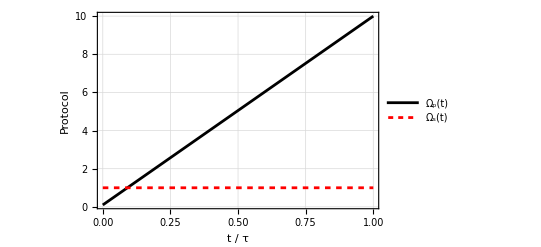

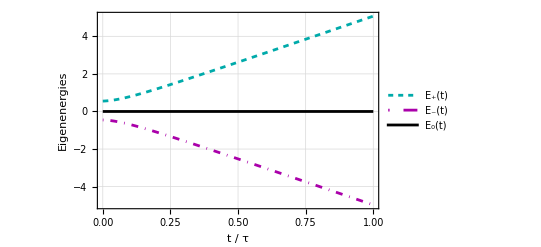

-Graphics-

```mathematica
tf = 1.0
Show[Plot[Ωp[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.86}]]]
Show[Plot[0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2] + 0.5*Δ, {t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Cyan], Dashing[0.01]},FrameLabel ->{"t / τ", "Eigenenergies"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_+(t)",10]},LegendLayout->"Row"],{Left,0.94}]],Plot[-0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2] + 0.5*Δ, {t,ti,tf},PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> {Darker[Magenta], DotDashed},FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_-(t)",10]},LegendLayout->"Row"],{Left,0.78}]], Plot[0,{t,ti,tf}, PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> Darker[Black],FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_0(t)",10]},LegendLayout->"Row"],{Left,0.86}]]]
Show[Plot[Ωp[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.86}]]]
```

## Minimal action

The protocols of the minimal action (MA) method comes from the minimization of the adiabatic action.

```mathematica
(*transitions between |n0 > and |n- > *)
ProtMA = Table[NDSolve[{D[ΩpMA'[t]/(ΩpMA[t]^2 + Ωs[t]^2),t] + 4*Δ/(ΩpMA[t]^2 + Ωs[t]^2)^(3/2)*(ΩpMA''[t] - 2.5*ΩpMA[t]*ΩpMA'[t]^2/(ΩpMA[t]^2 + Ωs[t]^2)) ==0 , ΩpMA[ti]==Ωpi, ΩpMA[tf]==Ωpf},ΩpMA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
(*transitions between |n0 > and |n+ >*)
ProtMA2 = Table[NDSolve[{D[ΩpMA2'[t]/(ΩpMA2[t]^2 + Ωs[t]^2),t] - 4*Δ/(ΩpMA2[t]^2 + Ωs[t]^2)^(3/2)*(ΩpMA2''[t] - 2.5*ΩpMA2[t]*ΩpMA2'[t]^2/(ΩpMA2[t]^2 + Ωs[t]^2)) ==0 , ΩpMA2[ti]==Ωpi, ΩpMA2[tf]==Ωpf},ΩpMA2,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
(*transitions between |n- > to |n+ >*)
(*ProtMA3 = Table[NDSolve[{D[ΩpMA3'[t]/(ΩpMA3[t]^2 + Ωs[t]^2),t] ==0 , ΩpMA3[ti]==Ωpi, ΩpMA3[tf]==Ωpf},ΩpMA3,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]*)
```

{{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}}}

{{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}}}

10

9.1

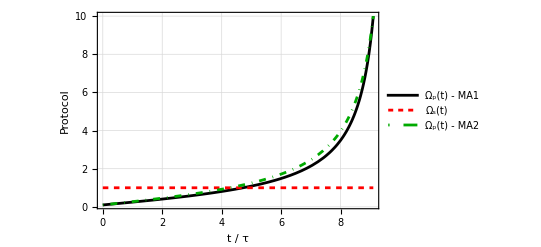

```mathematica
(*Protocol time for the Figure*)
n = 10
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - MA1",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.78}]],Plot[Evaluate[ΩpMA2[t]/.Flatten[Part[ProtMA2, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Green], DotDashed},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - MA2",10]},LegendLayout->"Row"],{Left,0.86}]](*,Plot[Evaluate[ΩpMA3[t]/.Flatten[Part[ProtMA3, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Yellow], DotDashed},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)- -+",10]},LegendLayout->"Row"],{Left,0.78}]]*)]
```

Solution of the Schrödinger equation for a system under the physical unitary transformation method.

```mathematica
SolMA = Table[NDSolve[{ⅈ*ℏ*c1MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c2MA[t],ⅈ*ℏ*c2MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c1MA[t]+(ℏ)*Δ*c2MA[t]+ (ℏ/2)*Ωs[t]*c3MA[t],ⅈ*ℏ*c3MA'[t] ==+(ℏ/2)*Ωs[t]*c2MA[t],c1MA[ti]==c10,c2MA[ti]==c20,c3MA[ti]==c30 },{c1MA,c2MA,c3MA},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
SolMA2 = Table[NDSolve[{ⅈ*ℏ*c1MA2'[t] ==(ℏ/2)*Evaluate[ΩpMA2[t]/.Flatten[Part[ProtMA2,(tf-Tmin)/ΔT + 1]]]*c2MA2[t],ⅈ*ℏ*c2MA2'[t] ==(ℏ/2)*Evaluate[ΩpMA2[t]/.Flatten[Part[ProtMA2,(tf-Tmin)/ΔT + 1]]]*c1MA2[t]+(ℏ)*Δ*c2MA2[t]+ (ℏ/2)*Ωs[t]*c3MA2[t],ⅈ*ℏ*c3MA2'[t] ==+(ℏ/2)*Ωs[t]*c2MA2[t],c1MA2[ti]==c10,c2MA2[ti]==c20,c3MA2[ti]==c30 },{c1MA2,c2MA2,c3MA2},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}}}

{{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}}}

Data for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the minimal action protocol.

```mathematica
(*Population transfer*)
pMA1 = Table[Abs[c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA2 = Table[Abs[c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA3 = Table[Abs[c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Population transfer 2*)
pMA12 = Table[Abs[c1MA2[t]/.Part[Flatten[Part[SolMA2,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA22 = Table[Abs[c2MA2[t]/.Part[Flatten[Part[SolMA2,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA32 = Table[Abs[c3MA2[t]/.Part[Flatten[Part[SolMA2,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Excess work*)
WexMA = Table[Wex[c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1]/.t->tf,c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2]/.t->tf,c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3]/.t->tf,Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]/.t->tf,Ωs[tf],Δ],{tf,Tmin,Tmax,ΔT}]
(*Time-averaged excess work*)
WexMAtimeaveraged= Table[NIntegrate[Wex[c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1],c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2],c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3],Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]],Ωs[t],Δ],{t,ti,tf}]/tf,{tf,Tmin,Tmax,ΔT}]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
CMA = Table[Cost[Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]],Ωs[t],0,Δ,tf],{tf,Tmin,Tmax,ΔT}]
```

{0.984324,0.447699,0.00245771,0.254952,0.353952,0.0687285,0.0429429,0.196271,0.118785,0.00856161,0.028211,0.0163213,0.00601649,0.0624424,0.0634334,0.0155817,0.0105549,0.00975924,0.00399338,0.0299885,0.039187,0.0166274,0.0111401,0.0117328,0.00551629,0.0165458,0.0252272,0.0152414,0.0130522,0.0149311,0.00816365}

{0.0056101,0.514576,0.836334,0.346296,0.0036999,0.156036,0.158128,0.00926271,0.0582222,0.104034,0.0226144,0.0126933,0.0404765,0.0083802,0.00989587,0.0356533,0.0133797,0.00318074,0.0179737,0.00664769,0.00228729,0.0164426,0.00874482,0.00120907,0.0100695,0.00561322,0.000420899,0.00858518,0.0061302,0.00059463,0.00629769}

{0.0100656,0.0377233,0.161207,0.398751,0.642348,0.775235,0.79893,0.794467,0.822994,0.887406,0.949175,0.970986,0.953507,0.929177,0.926671,0.948765,0.976066,0.98706,0.978033,0.963364,0.958526,0.96693,0.980115,0.987058,0.984414,0.977841,0.974352,0.976173,0.980817,0.984474,0.985538}

{0.982805,0.347866,0.0262545,0.416679,0.278666,0.00262628,0.220969,0.23323,0.0228052,0.043091,0.0412787,0.00431217,0.0928718,0.0851016,0.0119568,0.0195637,0.00852852,0.0129115,0.0568842,0.0367644,0.0105065,0.0162604,0.00518648,0.0174368,0.0355781,0.0182311,0.0140496,0.0156247,0.00637902,0.0168068,0.0210924}

{0.00710345,0.608924,0.784714,0.143639,0.0782302,0.288814,0.07534,0.0386222,0.16733,0.0541683,0.0152796,0.0721247,0.0147634,0.0200318,0.0558373,0.0102642,0.0139971,0.028708,0.00143571,0.016884,0.0228417,0.0013113,0.0134262,0.012041,0.000305156,0.0137192,0.00868556,0.001326,0.0112597,0.00418098,0.00193652}

{0.0100915,0.0432087,0.189029,0.439681,0.643103,0.70856,0.703692,0.728149,0.809865,0.902742,0.943442,0.923564,0.892365,0.894867,0.932206,0.970172,0.977474,0.95838,0.94168,0.946351,0.966652,0.982428,0.981387,0.970522,0.964116,0.968049,0.977264,0.983049,0.982361,0.979012,0.976971}

{-0.000498798,-0.0619064,-0.216977,-0.371295,-0.39768,-0.314745,-0.22923,-0.171381,-0.133569,-0.129777,-0.13694,-0.11305,-0.0696294,-0.0392852,-0.0299255,-0.0396682,-0.0552786,-0.0532325,-0.0330595,-0.0147672,-0.00925729,-0.0167057,-0.0292377,-0.031748,-0.0207085,-0.00820146,-0.00361508,-0.00820882,-0.0173229,-0.0208569,-0.0146378}

{-6.51827×10^-6,-0.00113351,-0.00625037,-0.0158737,-0.0251084,-0.0292049,-0.0282908,-0.0248116,-0.0205205,-0.0166992,-0.0141018,-0.012339,-0.0106773,-0.00895863,-0.00738578,-0.00617291,-0.00543186,-0.00500622,-0.00459416,-0.00407446,-0.00352706,-0.00307659,-0.00280291,-0.00266435,-0.00252768,-0.00231918,-0.00207127,-0.00185361,-0.0017176,-0.00165369,-0.00159532}

{1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548}

Figures for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the minimal action protocol.

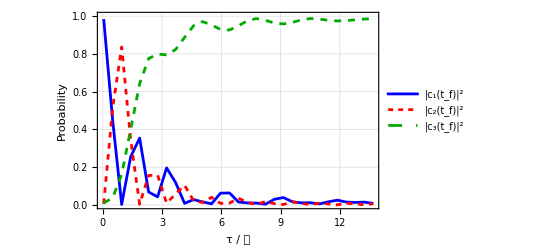

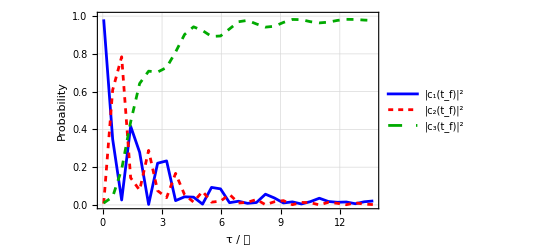

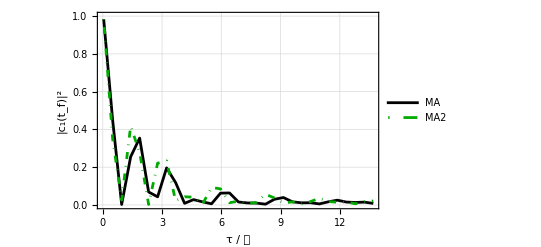

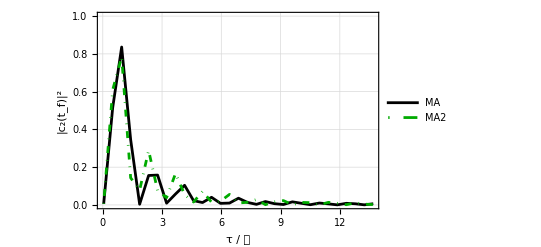

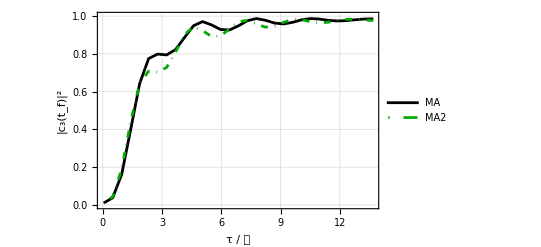

```mathematica
(*Population transfer*)
gMA = Show[ListPlot[Transpose[{time,pMA1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.92}]],ListPlot[Transpose[{time,pMA2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.84}]],ListPlot[Transpose[{time,pMA3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.76}]]]
gMA2 = Show[ListPlot[Transpose[{time,pMA12}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.92}]],ListPlot[Transpose[{time,pMA22}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.84}]],ListPlot[Transpose[{time,pMA32}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.76}]]]
(*MA Vs. MA2*)
Show[ListPlot[Transpose[{time,pMA1}], Joined->True,PlotStyle->{Black}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "|c_1(t_f)|^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pMA12}], Joined->True,PlotStyle->{Darker[Green], DotDashed}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA2",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[ListPlot[Transpose[{time,pMA2}], Joined->True,PlotStyle->{Black}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "|c_2(t_f)|^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pMA22}], Joined->True,PlotStyle->{Darker[Green], DotDashed}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA2",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[ListPlot[Transpose[{time,pMA3}], Joined->True,PlotStyle->{Black}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "|c_3(t_f)|^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.18}]],ListPlot[Transpose[{time,pMA32}], Joined->True,PlotStyle->{Darker[Green], DotDashed}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA2",10]},LegendLayout->"Row"],{Right,0.10}]]]
```

## Fast quasidiabatic

The protocols for the fast quasidiabatic method (FQ) can be found by solving the EDO generated when we make the adiabatic quantitative condition constant.

```mathematica
(*Transitions between |n0 > and |n- >*)
ProtFQ = Table[NDSolve[{D[ΩpFQ'[t]/(ΩpFQ[t]^2 + Ωs[t]^2)^(3/2)*(1+1.5*Δ/(ΩpFQ[t]^2 + Ωs[t]^2)^(1/2)),t] ==0 , ΩpFQ[ti]==Ωpi, ΩpFQ[tf]==Ωpf},ΩpFQ,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
(*Transitions between |n0 > and |n+ >*)
ProtFQ2 = Table[NDSolve[{D[ΩpFQ2'[t]/(ΩpFQ2[t]^2 + Ωs[t]^2)^(3/2)*(1-1.5*Δ/(ΩpFQ2[t]^2 + Ωs[t]^2)^(1/2)),t] ==0 , ΩpFQ2[ti]==Ωpi, ΩpFQ2[tf]==Ωpf},ΩpFQ2,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
(*Transitions between |n- > and |n+ >*)
(*ProtFQ3 = Table[DSolve[{D[ΩpFQ3[t]*ΩpFQ3'[t]/(ΩpFQ3[t]^2 + Ωs[t]^2)^(4/2),t] ==0 , ΩpFQ3[ti]==Ωpi, ΩpFQ3[tf]==Ωpf},ΩpFQ3,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]*)
```

{{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}}}

{{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}}}

Protocols for the fast quasidiabatic method.

10

9.1

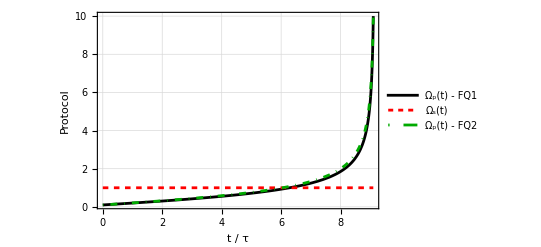

```mathematica
(*Protocol time for the Figure*)
n = 10
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - FQ1",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.78}]],Plot[Evaluate[ΩpFQ2[t]/.Flatten[Part[ProtFQ2, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Green],DotDashed},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - FQ2",10]},LegendLayout->"Row"],{Left,0.86}]](*,Plot[Evaluate[ΩpFQ3[t]/.Flatten[Part[ProtFQ3, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Green],Dashing[0.01]},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.78}]]*)]
```

Solution of the Schrödinger equation for the fast quasidiabatic protocol.

```mathematica
SolFQ = Table[NDSolve[{ⅈ*ℏ*c1FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c2FQ[t],ⅈ*ℏ*c2FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c1FQ[t]+(ℏ)*Δ*c2FQ[t]+ (ℏ/2)*Ωs[t]*c3FQ[t],ⅈ*ℏ*c3FQ'[t] ==+(ℏ/2)*Ωs[t]*c2FQ[t],c1FQ[ti]==c10,c2FQ[ti]==c20,c3FQ[ti]==c30 },{c1FQ,c2FQ,c3FQ},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
SolFQ2 = Table[NDSolve[{ⅈ*ℏ*c1FQ2'[t] ==(ℏ/2)*Evaluate[ΩpFQ2[t]/.Flatten[Part[ProtFQ2,(tf-Tmin)/ΔT + 1]]]*c2FQ2[t],ⅈ*ℏ*c2FQ2'[t] ==(ℏ/2)*Evaluate[ΩpFQ2[t]/.Flatten[Part[ProtFQ2,(tf-Tmin)/ΔT + 1]]]*c1FQ2[t]+(ℏ)*Δ*c2FQ2[t]+ (ℏ/2)*Ωs[t]*c3FQ2[t],ⅈ*ℏ*c3FQ2'[t] ==+(ℏ/2)*Ωs[t]*c2FQ2[t],c1FQ2[ti]==c10,c2FQ2[ti]==c20,c3FQ2[ti]==c30 },{c1FQ2,c2FQ2,c3FQ2},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}}}

{{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}}}

Data for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the fast quasidiabatic protocol.

```mathematica
(*Population transfer*)
pFQ1 = Table[Abs[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ2 = Table[Abs[c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ3 = Table[Abs[c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ12 = Table[Abs[c1FQ2[t]/.Part[Flatten[Part[SolFQ2,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ22 = Table[Abs[c2FQ2[t]/.Part[Flatten[Part[SolFQ2,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ32 = Table[Abs[c3FQ2[t]/.Part[Flatten[Part[SolFQ2,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Excess work*)
WexFQ = Table[Wex[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1]/.t->tf,c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2]/.t->tf,c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3]/.t->tf,Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]/.t->tf,Ωs[tf],Δ],{tf,Tmin,Tmax,ΔT}]
(*Time-averaged excess work*)
WexFQtimeaveraged= Table[NIntegrate[Wex[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1],c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2],c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3],Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]],Ωs[t],Δ],{t,ti,tf}]/tf,{tf,Tmin,Tmax,ΔT}]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
CFQ = Table[Cost[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]],Ωs[t],0,Δ,tf],{tf,Tmin,Tmax,ΔT}]
```

{0.988126,0.773281,0.376342,0.0847607,0.00582596,0.0298687,0.029864,0.00356382,0.0095346,0.048777,0.0686859,0.0477009,0.0173106,0.00608296,0.0065864,0.00428924,0.00458527,0.0158063,0.0282536,0.0278091,0.0174764,0.0103429,0.00957804,0.0088724,0.00704647,0.0090567,0.0145728,0.0170069,0.0143347,0.0117685,0.0123873}

{0.00187438,0.201766,0.534747,0.678754,0.532519,0.265283,0.079083,0.0165826,0.00742497,0.00741516,0.0265449,0.0625562,0.080296,0.0613493,0.0291423,0.0117339,0.00851454,0.00648562,0.00605111,0.0134925,0.0227782,0.022548,0.0140434,0.00794497,0.00753847,0.00710242,0.00455545,0.00429984,0.00746979,0.00914526,0.00702681}

{0.00999996,0.0249519,0.0889094,0.236484,0.461653,0.704848,0.891052,0.979853,0.983041,0.943808,0.904769,0.889742,0.902392,0.932567,0.964271,0.983977,0.9869,0.977708,0.965695,0.958698,0.959745,0.967109,0.976378,0.983182,0.985415,0.983841,0.980872,0.978693,0.978195,0.979086,0.980586}

{0.987821,0.742949,0.313416,0.0424072,0.0151454,0.0606053,0.0426989,0.00242654,0.0179868,0.0643177,0.0711837,0.0361448,0.00877553,0.0063144,0.00668328,0.00256541,0.00923947,0.0261759,0.0327204,0.0224969,0.011304,0.00909595,0.00902437,0.00660641,0.00799858,0.0148586,0.0186982,0.015448,0.0117188,0.012178,0.0126725}

{0.00217101,0.230708,0.589348,0.698066,0.484558,0.191525,0.0351719,0.00751373,0.00575725,0.00394255,0.0302163,0.0687651,0.0729807,0.0410922,0.0130785,0.00703263,0.0067486,0.00333915,0.00707153,0.0187247,0.0230491,0.0148515,0.00659217,0.00602394,0.00656586,0.00364164,0.00277596,0.00667453,0.00904016,0.00636021,0.00385272}

{0.0100075,0.0263425,0.097235,0.259525,0.500295,0.747868,0.922129,0.99006,0.976256,0.93174,0.8986,0.89509,0.918243,0.952593,0.980238,0.990402,0.984012,0.970485,0.960208,0.958778,0.965647,0.976052,0.984383,0.98737,0.985436,0.9815,0.978526,0.977877,0.979241,0.981462,0.983475}

{-0.000602043,-0.0690733,-0.217925,-0.372674,-0.457723,-0.43401,-0.313797,-0.147069,0.00633262,0.100176,0.114071,0.0577447,-0.0322286,-0.107452,-0.131567,-0.0984133,-0.0314972,0.0329452,0.0656497,0.0561126,0.0144866,-0.0347918,-0.0656267,-0.0639229,-0.0341438,0.00535556,0.0339355,0.0391542,0.0213574,-0.00794662,-0.0325235}

{-3.36497×10^-6,-0.000441756,-0.00186597,-0.00454012,-0.00804941,-0.0111971,-0.0126666,-0.0118551,-0.00918399,-0.00575283,-0.00272407,-0.00085932,-0.000345351,-0.00085379,-0.00175945,-0.00244235,-0.00254862,-0.00208561,-0.00132879,-0.000631415,-0.000250885,-0.000256146,-0.000530908,-0.00085755,-0.00103772,-0.000985438,-0.000746987,-0.000451392,-0.000232686,-0.000166405,-0.000243809}

{1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191}

Figures for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the fast quasidiabatic protocol.

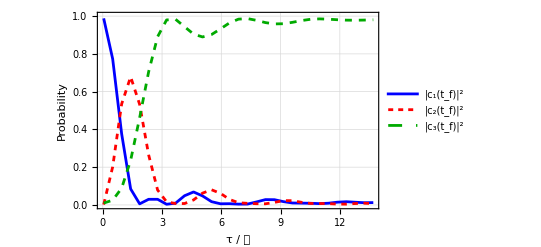

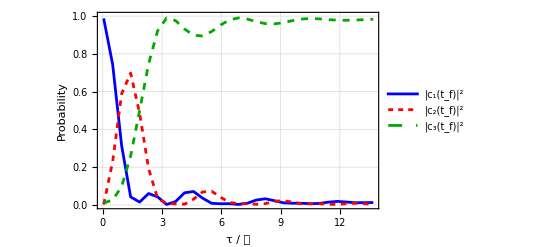

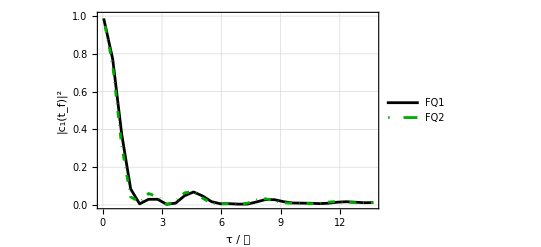

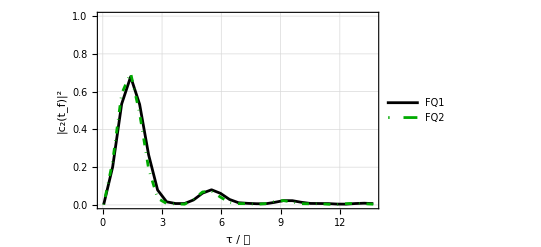

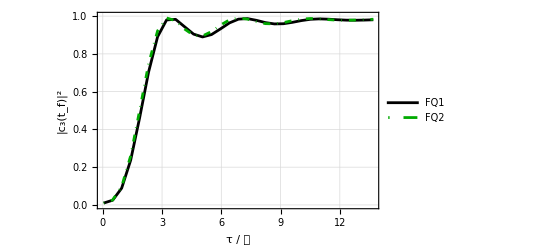

```mathematica
(*Population transfer*)
gFQ = Show[ListPlot[Transpose[{time,pFQ1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.92}]],ListPlot[Transpose[{time,pFQ2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.84}]],ListPlot[Transpose[{time,pFQ3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.76}]]]
gFQ2 = Show[ListPlot[Transpose[{time,pFQ12}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.92}]],ListPlot[Transpose[{time,pFQ22}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.84}]],ListPlot[Transpose[{time,pFQ32}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.76}]]]
Show[ListPlot[Transpose[{time,pFQ1}], Joined->True,PlotStyle->{Black}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "|c_1(t_f)|^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ1",10]},LegendLayout->"Row"],{Right,0.94}]], 
ListPlot[Transpose[{time,pFQ12}], Joined->True,PlotStyle->{Darker[Green], DotDashed}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ2",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[ListPlot[Transpose[{time,pFQ2}], Joined->True,PlotStyle->{Black}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "|c_2(t_f)|^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ1",10]},LegendLayout->"Row"],{Right,0.94}]], 
ListPlot[Transpose[{time,pFQ22}], Joined->True,PlotStyle->{Darker[Green], DotDashed}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "|c_2(t_f)|^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ2",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[ListPlot[Transpose[{time,pFQ3}], Joined->True,PlotStyle->{Black}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "|c_3(t_f)|^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ1",10]},LegendLayout->"Row"],{Right,0.18}]],ListPlot[Transpose[{time,pFQ32}], Joined->True,PlotStyle->{Darker[Green], DotDashed}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "|c_3(t_f)|^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ2",10]},LegendLayout->"Row"],{Right,0.10}]]]
```